```mathematica
E^(I y)-Cos[I y]
```

ⅇ^(ⅈ y)-Cosh[y]

-Graphics3D-

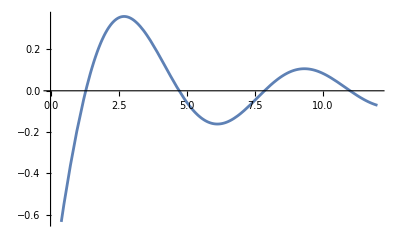

-1+z-z^2/6-z^4/120+z^5/360-z^6/5040-z^8/362880+z^9/1814400-z^10/39916800-z^12/6227020800+O[z]^13

```mathematica
Clear[f,z]
f[z_]:= (ⅇ^-z-Cos[z])/z
ComplexPlot3D[f[z],{z,2}]
Plot[f[x],{x, 0, 12}]
Series[f[z],{z, 0, 12}]
```

## Bessel J HW

The J_n HW was causing folks to work harder than they needed to.  Here is what I would have done.
a) Only singularity of f=ⅇ^(t/2(z-1/z)) is an essential singularity at z=0. 
b) To verify that two expressions full of derivatives are equal just compute them both carefully and tidy as you go. Since
	z ∂_z f=(z t)/2 f  (1+1/z^2)=t/2 f  (z+1/z)
we have
	z ∂_z (z ∂_z f)=z t/2( ∂_z f+f(1-1/z^2))=(z t)/2( t/2 f  (1+1/z^2)+f(1-1/z^2))=(t^2/2+t^2/(4 z^2)-t/(2 z)+(t z)/2+(t^2 z^2)/4 ) f
Similarly (but simpler) we have 
	(∂^n f)/(∂t^n)=f (z-1/z)^n/2^n
so
	t^2(∂^2 f)/(∂t^2)+t(∂^2 f)/(∂t^2)+t^2 f=(t^2(z-1/z)^2/2^2+t(z-1/z)^1/2^1+t^2)f=f(t^2/2+t^2/(4 z^2)-t/(2 z)+(t z)/2+(t^2 z^2)/4).
They match so we have checked the thing they wanted.
c) The point of all this is that since f=∑_(n=-∞)^∞ J_n(t)z^nwe have that 
	t^2(∂^2 f)/(∂t^2)+t(∂^2 f)/(∂t^2)+t^2 f=∑_(n=-∞)^∞ (t^2 J_n''+t J_n'+t^2 J_n)z^n
while 
	z ∂_z (z ∂_z f)=z ∂_z (∑_(n=-∞)^∞ z J_n(t)n z^(n-1))=z ∂_z (∑_(n=-∞)^∞ J_n(t)n z^n)=z(∑_(n=-∞)^∞ J_n(t)n n z^(n-1))=∑_(n=-∞)^∞ J_n(t)n^2 z^n
Since the two expressions match and Laurent series are unique the coefficients must match and
	t^2 J_n''+t J_n'+t^2 J_n=n^2 J_n
which is the Bessel ODE 
	t^2 J_n''(t)+t J_n'(t)+(t^2-n^2)J_n(t)=0.
In other words, the Laurent coefficients of f satisfy the Bessel ODE.  
d) The last part uses the general expression
	a_n=1/(2π ⅈ)∫_Γ (f(z))/(z-z_0)^(n+1)dz
for the Laurent series coefficients from p108.  For our ourf=ⅇ^(t/2(z-1/z))=ⅇ^(z/(2t))ⅇ^(-t/(2 z)) all we need is a contour that goes round the essential singularity at z_0=0.  The easiest contour is a tiny circle p(θ)=ϵ ⅇ^(ⅈ  θ) for 0≤θ≤2π.  On this circle as ϵ->0 
	ⅇ^(z/t)=ⅇ^(ϵ ⅇ^(ⅈ θ))->ϵ^0=1
Since the TS of ⅇ^u=1+u+u^2/(2!)+… we have 
	ⅇ^(t/(2z))=1+t/(2 z)+(t/(2 z))^2 1/(2!)+…
and we have 
	a_n=1/(2π ⅈ)∫_Γ (f(z))/(z-z_0)^(n+1)dz=1/(2π ⅈ)∫_0^(2π) (1+t/(2 z)+…)

```mathematica
Normal[Series[ⅇ^u,{u,0,3}]]/.u->t/(2 ϵ ⅇ^ⅈθ)
```

1+(ⅇ^(-3 ⅈθ) t^3)/(48 ϵ^3)+(ⅇ^(-2 ⅈθ) t^2)/(8 ϵ^2)+(ⅇ^-ⅈθ t)/(2 ϵ)

We can then evaluate
	J_n(t)=1/(2π ⅈ)(∫_0)^(2π)(ⅇ^(t/2(ϵ ⅇ^(ⅈ θ)-1/ϵ ⅇ^(-ⅈ θ))))/((ⅇ^(ⅈ θ))^(n+1))ⅈ ⅇ^(ⅈ θ)dθ=1/(2 π)(∫_0)^(2π)ⅇ^(t/2 ⅇ^(ⅈ θ)- t/2 ⅇ^(-ⅈ θ)) ⅇ^(-ⅈ n θ)dθ=1/(2 π)(∫_0)^(2π)ⅇ^(t/2 ⅇ^(ⅈ θ)- t/2 ⅇ^(-ⅈ θ)-ⅈ n θ) dθ

```mathematica
Simplify[(ⅇ^(t/2(ⅇ^(ⅈ θ)-ⅇ^(-ⅈ θ))))/((ⅇ^(ⅈ θ))^(n+1))ⅈ ⅇ^(ⅈ θ)]
```

ⅈ ⅇ^(1/2 ⅇ^(-ⅈ θ) (-1+ⅇ^(2 ⅈ θ)) t) (ⅇ^(ⅈ θ))^-n

```mathematica
f[z_,t_]:=ⅇ^(t/2(z-1/z))
z Simplify[D[z D[f[z,t],z],z]]/. ⅇ^z
```

```mathematica
Expand[(t (2 z (-1+z^2)+t (1+z^2)^2))/(4 z^2)]
```

t^2/2+t^2/(4 z^2)-t/(2 z)+(t z)/2+(t^2 z^2)/4

```mathematica
Expand[(t^2(z-1/z)^2/2^2+t(z-1/z)^1/2^1+t^2)]
```

t^2/2+t^2/(4 z^2)-t/(2 z)+(t z)/2+(t^2 z^2)/4

```mathematica
f[z_]:=(√(1-z^2))/(1+z^2)
F[z_]=Integrate[f[z],z]
ComplexPlot3D[f[z],{z,2}]
ComplexPlot3D[F[z],{z,2}]
```

√2 ArcTan[(√2 z)/(√(1-z^2))]+2 ArcTan[(√(1-z^2))/(1+z)]

-Graphics3D-

-Graphics3D-

```mathematica
f[z_]:=√(1-z^2)
ComplexPlot3D[f[z],{z,2},
PlotLegends->Automatic,
Mesh->Automatic]
```

-Graphics3D-

```mathematica
?ArcTan
```

```mathematica
f[z_]:=(1-z)√(1-z^2)
ComplexPlot3D[f[z],{z,2},
PlotLegends->Automatic,
Mesh->Automatic]
```

-Graphics3D-

```mathematica
f[z_]:=ArcTan[(√(1-z^2))/(1+z)]
ComplexPlot3D[f[z],{z,2},
PlotLegends->Automatic,
Mesh->Automatic]
```

-Graphics3D-